## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initialize Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="ENO";
fitLabel=rxnName;
dataFileName="ENO";

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
(*Q10 = 2.5; Average factor for biological systems*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "ENO_param_inf";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/PhD_stuff/Projects/MD/eMASS-MD/enzyme_models/ENO/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 330 | 313.5
346.5 | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((2pg)^c⇌h2o^c+pep^c)^ENO

Null; Null

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg,Null | 5.19 | 4.9305
5.4495 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | 0.0001 | 0.000095
0.000105 | mg2 | 0.001
so4 | 0.001 | M | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 2pg | Null | 330 | 313.5
346.5 | 1/s | 8.1 | 30 | trishcl | 0.05 | cl | 0.1
k | 0.1

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_ENO[c] + 2pg[c] <=> E_ENO[c]&2pg",
				"E_ENO[c]&2pg <=> E_ENO[c]&pep",
				"E_ENO[c]&pep <=> E_ENO[c] + pep[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModel["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1}
```

{{((ENO^c)_^+(2pg)^c⇌(ENO^c&(2pg)^c)_^)^ENO1,((ENO^c&pep^c)_^⇌(ENO^c)_^+pep^c)^ENO2,((ENO^c&(2pg)^c)_^⇌(ENO^c&pep^c)_^)^ENO3}}

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
(* for the flux equation regarding product inhibition *)
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList,
						 otherMetsReverseZeroSub, otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(2pg)^c→0}

{pep^c→0}

{(2pg)^c→∞}

{pep^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
rateConstsSub
```

{k_ENO1^⟵→x<0>,k_ENO1^⟶→x<1>,k_ENO2^⟵→x<2>,k_ENO2^⟶→x<3>,k_ENO3^⟵→x<4>,k_ENO3^⟶→x<5>}

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{1.0,( Subscript[k, ENO1]^⟶/Subscript[k, ENO1]^⟵)*(Subscript[k, ENO2]^⟶/Subscript[k, ENO2]^⟵), 1.75*10^-6,{4.9*10^-16, 6232}}}; (*Define dKb ratio and respective value*)
customRatiosDataList;
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

{0.113075}

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/haldaneRatio_1.txt"	5.19
1	0.00001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/relRateFor_2pg.txt"	0.9090909090909091
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/absRateFor.txt"	330
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_inf/input/customRatio_1.txt"	1.75e-6

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter influence

```mathematica
dataFileName = "ENO_all";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "ENO_dKd";
KeqListTemp=KeqList;
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp={};

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "ENO_Keq";
KeqListTemp={};
kmListTemp= kmList;
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "ENO_Km";
KeqListTemp=KeqList;
kmListTemp={};
kcatListTemp = kcatList;
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];

dataFileName = "ENO_kcat";
KeqListTemp=KeqList;
kmListTemp=kmList;
kcatListTemp = {};
customRatiosDataListTemp=customRatiosDataList;

{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,  haldaneRatiosList, KeqListTemp, kmListTemp, s05List, kcatListTemp, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataListTemp];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating custom ratios data...

### Parameter scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,1.75*10^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
Length@dataPathList
```

26

```mathematica
FilePrint[dataPathList[[26]]]
```

Priority	2pg[c]	pep[c]	param_ENO_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/haldaneRatio_1.txt"	5.19
1	0.00001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.09090909090909091
1	0.00001584893192461114	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.13680688860321005
1	0.000025118864315095822	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.20076000891310186
1	0.000039810717055349695	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.2847472489508013
1	0.00006309573444801929	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.3868631798468568
1	0.0001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.5
1	0.00015848931924611142	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.6131368201531432
1	0.0002511886431509582	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.7152527510491988
1	0.00039810717055349735	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.7992399910868982
1	0.000630957344480193	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.8631931113967899
1	0.001	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/relRateFor_2pg.txt"	0.9090909090909091
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1	0.01	0	1	8.1	30	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/absRateFor.txt"	330
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12
1.	0	0	1	7.5	25	"/home/mrama/Desktop/MD/kinetics/ENO/ENO_param_scan/input/customRatio_1.txt"	1.e12

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.466236720111
best_fit: 0.709733944854
best_fit: 0.965976414563
best_fit: 0.933230755064
best_fit: 0.983256514782
best_fit: 0.923000756654
best_fit: 0.754737981175
best_fit: 0.989349481383
best_fit: 0.965544255486
best_fit: 0.805629811654
best_fit: 0.650895939147
best_fit: 0.488692634496
best_fit: 0.939150625096
best_fit: 1.05606522416
best_fit: 1.09659920063
best_fit: 0.776447034824
best_fit: 0.467742035241
best_fit: 0.794865506855
best_fit: 1.09641390824
best_fit: 0.807642751354
best_fit: 0.206496650535
best_fit: 0.528967814162
best_fit: 0.863385116912
best_fit: 0.889059257604
best_fit: 0.68617247437
best_fit: 0.552473224612
best_fit: 0.918236515992
best_fit: 0.58749754888
best_fit: 0.663722831221
best_fit: 0.671100350727
best_fit: 0.912432747242
best_fit: 0.95355132923
best_fit: 1.09273812846
best_fit: 0.863720297121
best_fit: 0.681837809574
best_fit: 0.399071670315
best_fit: 1.01511828003
best_fit: 0.668219107333
best_fit: 0.502736795718
best_fit: 1.06055323655
best_fit: 0.927082620284
best_fit: 0.662652502491
best_fit: 0.767272150013
best_fit: 0.996781374487
best_fit: 0.0865519381694
best_fit: 0.64459259168
best_fit: 0.563226009315
best_fit: 0.902221946459
best_fit: 0.753331800223
best_fit: 0.881371813871
best_fit: 0.765017078188
best_fit: 0.643102952942
best_fit: 0.792463506669
best_fit: 1.07343402948
best_fit: 0.979842003711
best_fit: 0.4106461746
best_fit: 0.679886993734
best_fit: 0.718845599674
best_fit: 0.50981610548
best_fit: 0.453971215427
best_fit: 1.09164924102
best_fit: 1.00748431727
best_fit: 1.02259219859
best_fit: 0.863515347556
best_fit: 0.686761818993
best_fit: 0.688995318979
best_fit: 0.873780195935
best_fit: 0.101428155814
best_fit: 1.05214131272
best_fit: 0.976196277567
best_fit: 1.04698845368
best_fit: 1.04748910297
best_fit: 1.07574435172
best_fit: 0.918360598201
best_fit: 0.83933739888
best_fit: 0.919404378493
best_fit: 1.09916538116
best_fit: 0.493352798136
best_fit: 0.415292418473
best_fit: 0.0969409957847
best_fit: 0.99714471065
best_fit: 0.386580095136
best_fit: 0.809953685721
best_fit: 0.164787517043
best_fit: 1.09344762856
best_fit: 0.956040893657
best_fit: 1.01481877654
best_fit: 0.934542618104
best_fit: 0.931455832819
best_fit: 0.434975272524
best_fit: 0.265771925635
best_fit: 0.948292247915
best_fit: 1.06554538321
best_fit: 0.37474475929
best_fit: 1.06414742738
best_fit: 0.468691196639
best_fit: 0.950298044432
best_fit: 1.0450365
best_fit: 0.49514405799
best_fit: 0.736222814961

## Evaluate fit results for param_scan

```mathematica
paramScanList={{"customRatio",1,{10.^-12,10.^-11,10.^-10,10.^-9,10.^-8, 10.^-7,10.^-6,1.75*10^-6,10.^-5,0.0001,0.001, 0.01,0.1, 1.0,  10, 100, 1000, 10000, 10^5,10^6,10^7, 10^8, 10^9, 10^10,10^11,10^12}}};

nEnsembles = 10;

flagFitType = "abs_ssd";
errorList = {};

Do[
Do[
fitDescription = paramScan[[1]] <>"_"<>ToString[paramScan[[2]]]<>"_"<> ToString[N@AccountingForm[paramVal]];

ssdList = 
Table[

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> "_"<>ToString@ensembleI<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "ENO_"<> fitDescription<>".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];
Print@{paramVal, filteredDataList[[1,1]]};
ToString[N@AccountingForm[filteredDataList[[1,1]]]],

{ensembleI, Range[nEnsembles]}];

Print[ssdList];
AppendTo[errorList, Flatten@{ToString[N@AccountingForm[paramVal]], ssdList}];,

{paramVal, paramScan[[3]]}];,
{paramScan, paramScanList}];

Export[ FileNameJoin[{outputPath, "treated_data", "param_scan_ssd.csv"}, OperatingSystem->$OperatingSystem],errorList, "TSV"];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | haldaneRatio_1 | 3.08458×10^-10 | 9.51466×10^-20 | 3.68621×10^-9 | 7.10252×10^-8 | 5.19 | 5.19
1 | relRateFor_2pg | 4.72843×10^-7 | 2.2358×10^-13 | 9.89783×10^-8 | 0.000108876 | 0.0909091 | 0.0909092
1 | relRateFor_2pg | 4.4897×10^-7 | 2.01574×10^-13 | 1.4143×10^-7 | 0.000103379 | 0.136807 | 0.136807
1 | relRateFor_2pg | 4.15706×10^-7 | 1.72812×10^-13 | 1.92167×10^-7 | 0.00009572 | 0.20076 | 0.20076
1 | relRateFor_2pg | 3.72022×10^-7 | 1.38401×10^-13 | 2.43918×10^-7 | 0.0000856614 | 0.284747 | 0.284747
1 | relRateFor_2pg | 3.18909×10^-7 | 1.01703×10^-13 | 2.8408×10^-7 | 0.0000734316 | 0.386863 | 0.386863
1 | relRateFor_2pg | 2.60064×10^-7 | 6.76331×10^-14 | 2.99409×10^-7 | 0.0000598819 | 0.5 | 0.5
1 | relRateFor_2pg | 2.01218×10^-7 | 4.04887×10^-14 | 2.8408×10^-7 | 0.0000463322 | 0.613137 | 0.613137
1 | relRateFor_2pg | 1.48105×10^-7 | 2.1935×10^-14 | 2.43918×10^-7 | 0.0000341024 | 0.715253 | 0.715253
1 | relRateFor_2pg | 1.04421×10^-7 | 1.09037×10^-14 | 1.92167×10^-7 | 0.0000240438 | 0.79924 | 0.79924
1 | relRateFor_2pg | 7.1157×10^-8 | 5.06331×10^-15 | 1.4143×10^-7 | 0.0000163845 | 0.863193 | 0.863193
1 | relRateFor_2pg | 4.72843×10^-8 | 2.2358×10^-15 | 9.89782×10^-8 | 0.0000108876 | 0.909091 | 0.909091
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1 | absRateFor | 3.79521×10^-9 | 1.44036×10^-17 | 2.8838×10^-6 | 8.73879×10^-7 | 330 | 330.
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6
1. | customRatio_1 | 0.304951 | 0.0929954 | 1.78175×10^-6 | 101.814 | 1.75×10^-6 | 3.53175×10^-6

### Simulated Data and Best Fit Data Plot

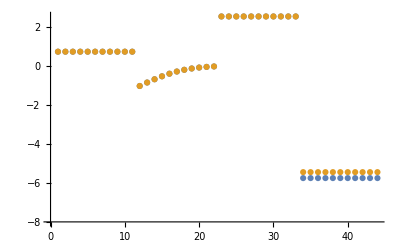

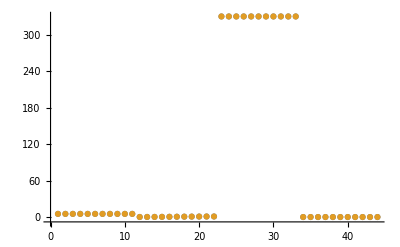

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10

## Evaluate fit results for param_inf

```mathematica
paramList={"all", "dKd", "kcat", "Keq", "Km"};
nEnsembles = 99;

flagFitType = "abs_ssd";

Do[
Do[

fitDescription = param <>"_"<>ToString[fitI];

lmaResultsFileNew = FileNameJoin[{outputPath, "raw", "lmaResults_"<> fitDescription<> ".txt"}, OperatingSystem->$OperatingSystem];
dataFilePath  = FileNameJoin[{inputPath,  "ENO_"<> param<> ".dat"}, OperatingSystem->$OperatingSystem];

{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitDescription];,

{fitI, 0, nEnsembles}],
{param, paramList}];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | haldaneRatio_1 | 2.15415×10^-11 | 4.64038×10^-22 | 2.57431×10^-10 | 4.96013×10^-9 | 5.19 | 5.19
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1 | absRateFor | 2.37785×10^-9 | 5.65419×10^-18 | 1.80682×10^-6 | 5.47521×10^-7 | 330 | 330.
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6
1. | customRatio_1 | 0.092334 | 0.00852557 | 4.14572×10^-7 | 23.6898 | 1.75×10^-6 | 2.16457×10^-6

### Simulated Data and Best Fit Data Plot

```mathematica
fitI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[fitI,3]]}, AxesOrigin->{0,-8}]
```

-Graphics-

-Graphics-

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

-Graphics-

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

-Graphics-

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

-Graphics-

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

-Graphics-

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10